```mathematica
OptimizationMatrix[J_, h_]:={{-h^2 - (1/2)J^2, h*J, -(1/8)J^2},{2*h*J, -h^2-J^2, 0.5 * h*J},{-2*J^2, 4*h*J, -h^2-(1/2)J^2}};
OptimizationVector[J_, h_]:={-h, J, 0};
J = 1.0;
MatrixForm[OptimizationMatrix[J, 1]]
```

(-1.5 | 1. | -0.125
2. | -2. | 0.5
-2. | 4. | -1.5)

```mathematica
Eigenvalues[OptimizationMatrix[J,1]]
```

{-4.,-1.,1.13756×10^-17}

```mathematica
alpha[h_]:=Dot[Inverse[OptimizationMatrix[J, h]],OptimizationVector[J, h]][[1]];
beta[h_]:=Dot[Inverse[OptimizationMatrix[J, h]],OptimizationVector[J, h]][[2]];
gamma[h_]:=Dot[Inverse[OptimizationMatrix[J, h]],OptimizationVector[J, h]][[3]];

Simplify[alpha[h]]
Simplify[beta[h]]
Simplify[gamma[h]]
```

0.-(1. h^3)/(0.+1. h^2-2. h^4+h^6)+(h (0.5-0.5 h^2+h^4))/(0.+1. h^2-2. h^4+h^6)

0.-(1. h^2)/(0.+1. h^2-2. h^4+h^6)+(1. h^4)/(0.+1. h^2-2. h^4+h^6)

0.-(2. h)/(0.+1. h^2-2. h^4+h^6)+(2. h^3)/(0.+1. h^2-2. h^4+h^6)

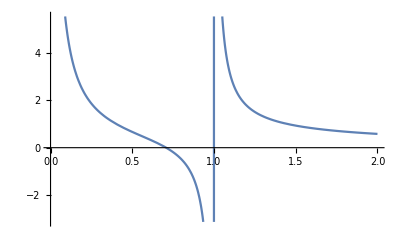

```mathematica
Plot[0.-(1. h^3)/(0.+1. h^2-2. h^4+h^6)+(h (0.5-0.5 h^2+h^4))/(0.+1. h^2-2. h^4+h^6),{h,0,2}]
```

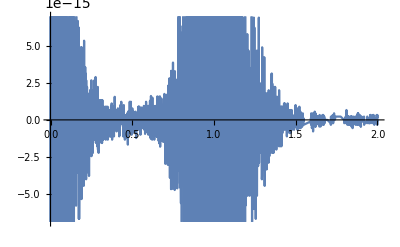

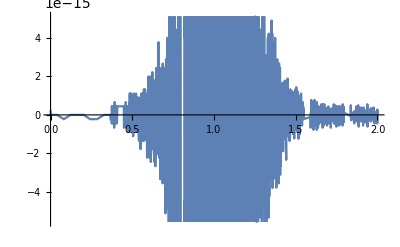

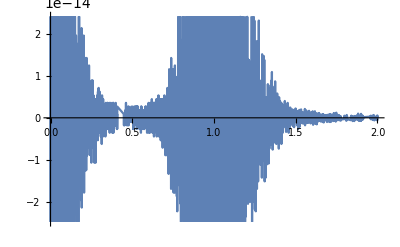

```mathematica
Plot[alpha[h]-(0.5-1.5*h^2 +h^4)/(h*(1-h^2 )^2 ),{h,0,2}]
Plot[beta[h]-(-1.)/(1-h^2  ),{h,0,2}]
Plot[gamma[h]-(-2.)/(h*(1-h^2 )),{h,0,2}]
```

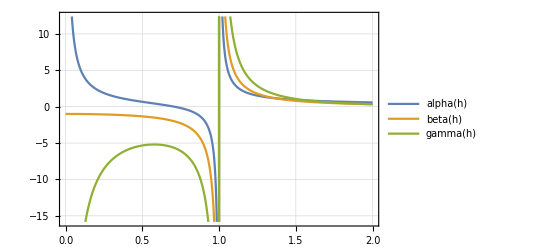

```mathematica
Plot[{alpha[h],beta[h],gamma[h]},{h,0.,2.},PlotTheme->"Detailed"]
```